# Energy Transfer by Gravitational Induction

This notebook contains the code for setting up a gravitational induction experiment, as described by Hermann Bondi and William McCrea in their paper “Energy transfer by gravitation in Newtonian theory” . Two example uses are provided; plotting the energy density flux, and integrating said flux over a surface.

Author: Tobias Eklund (tobias.eklund@protonmail.com)

This work is part of the the author’s 2021 MSc thesis “Local Energy in Newtonian Gravitation”, supervised by Ingemar Bengtsson at Stockholm University.

Reference
Bondi, H., & McCrea, W. (1960). Energy transfer by gravitation in Newtonian theory. Mathematical Proceedings of the Cambridge Philosophical Society, 56(4), 410-413. doi:10.1017/S0305004100034721

Definitions

```mathematica
(*Potential of the whole system.*)
(*The vector r is the place of evaluation*)
V[r_,t_]:=Mt Um[r+ m/Mt dvec[t] ]+Qt[t] Uq[r+m/Mt dvec[t]] + Mr Um[r-m/Mr dvec[t]] + Qr[t] Uq[r-m/Mr dvec[t]]
```

```mathematica
(*Reduced mass.*)
m=Mt Mr/(Mt + Mr);
```

```mathematica
(*Potential per monopole moment*)
Um[x_]:=-1/norm[x]
```

```mathematica
(*Potential per quadrupole moment, x[[3]]/norm[x] = Cos[theta] if x[3]=z.*)
Uq[x_]:=- LegendreP[2,x[[3]]/norm[x]]/(norm[x]^3)
```

```mathematica
(*Norm of a vector. Mathematica fails to differentiate it's own routine Norm[x], so it had to be reimplemented.*)
norm[x_]:=Sqrt[x[[1]]^2+x[[2]]^2+x[[3]]^2]
```

```mathematica
(*Transmitter quadropole moment.*)
(*This is the condition for Kepler orbits.*)
Qt[t_]:=- 2 Mt /(2 Mr - 15 Qr[t]/d[t]^2) Qr[t]
```

```mathematica
(*Receiver quadrupole moment.*)
(*This choice gives positive net transfer to receiver if Qrmax >0.*)
Qr[t_]:=-Qrmax Sin[γ[t]]
```

```mathematica
(*Separation vector between transmitter and receiver.*)
dvec[t_]:=d[t]{Cos[γ[t]],Sin[γ[t]],0}
```

```mathematica
(*Length of the separation vector.*)
(*This makes the trajectory an ellipse.*)
(*The parameter e is the orbit eccentricity*)
d[t_]:=dmin (1+e )/(1+e Cos[γ[t]])
```

```mathematica
(*The time derivative γ'[t] is known due to conserved angular momentum l.*)
(*Defining the derivative in this way, it is automatically substituted as the symbol γ'
is encountered by Mathematica.*)
γ'[t_]:=l/d[t]^2
```

```mathematica
(*The general vacuum energy density flux vector for Newtonian gravitation*)
S[r_,t_]:=n*1/(8Pi )(V[r,t] Grad[D[V[r,t],t],r]-D[V[r,t],t]Grad[V[r,t],r])-(n-1)1/(4 Pi) V[r,t] Grad[D[V[r,t],t],r]
```

## Getting usable expressions

```mathematica
(*Perform the necessary differentiations (w.r.t time and space) by evaluating for an input vector {x,y,z}*)
(*This provides an expression depending on dmin, γ[t], Mr, Mt, e, l, Qrmax, and n.*)
Seval=S[{x,y,z},t];
```

```mathematica
(*Choose some parameter values.*)
params={Mr->1,Mt->1 ,dmin->1,Qrmax->1/10,l->1,e->1/2};
```

```mathematica
(*It is now possible to compute a result. For example, at the periapsis (γ[t]=0).*)
Speriapsis=Seval//.params//.γ[t]->0;
```

```mathematica
(*The vector value at the origin is*)
Speriapsis//.{x->0,y->0,z->0}
```

{-(24 (-1+n))/(5 π)+(12 n)/(5 π),0,0}

```mathematica
(*As an important sidenote, the result during the periapsis is independent of orbit eccentricity.*)
D[Speriapsis,e]
```

{0,0,0}

## Plotting the vector fields

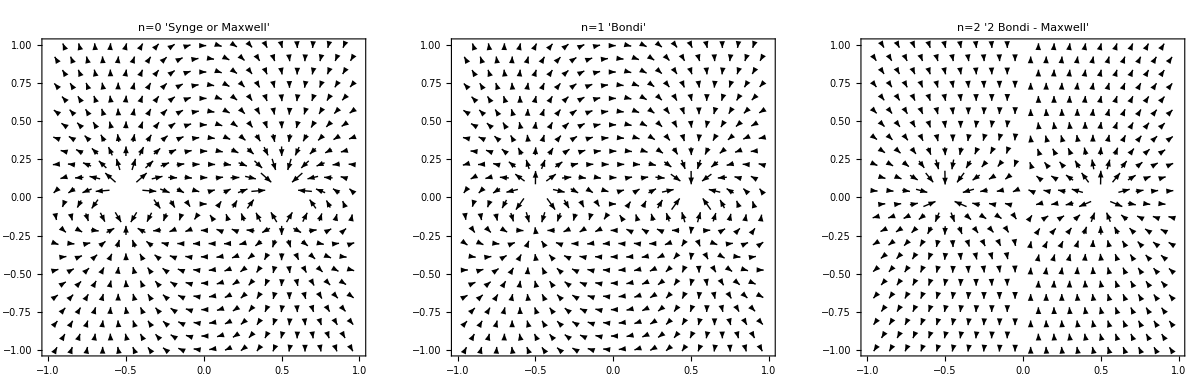

```mathematica
(*The command below plots the three main types of energy density flux during the periapsis, over the plane z=0.*)
scaling="Log";
clip=500;
points=20;
plotrange=1;
options={VectorScaling->scaling,  VectorColorFunction->None,VectorStyle->Black,VectorPoints->points,VectorRange->{0,clip},ClippingStyle->None};
(*The case n=0, Bondi's energy flux.*)
S0peri=VectorPlot[Speriapsis[[{1,2}]]//.{n->0,z->0},{x,-plotrange,plotrange},{y,-plotrange,plotrange}, Evaluate[options], PlotLabel->"n=0 'Synge or Maxwell'"];S1peri=VectorPlot[Speriapsis[[{1,2}]]//.{n->1,z->0},{x,-plotrange,plotrange},{y,-plotrange,plotrange}, Evaluate[options], PlotLabel->"n=1 'Bondi'"];S2peri=VectorPlot[Speriapsis[[{1,2}]]//.{n->2,z->0},{x,-plotrange,plotrange},{y,-plotrange,plotrange}, Evaluate[options], PlotLabel->"n=2 '2 Bondi - Maxwell'"];
GraphicsRow[{S0peri,S1peri,S2peri},ImageSize->Full]
(*The results are complicated and hard to interpret. They all seem to be dominated by energy flux related to the orbital motion (anti-clockwise rotation)*)
```

## Surface integral (n=0)

```mathematica
(*Bondi's flux density is divergence-free in the vacuum.*)
Div[Speriapsis//.n->1,{x,y,z}]//Simplify
```

0

```mathematica
(*But this is not true about the other two.*)
Divperi=Div[Speriapsis//.n->0,{x,y,z}]//Simplify
```

1/(5 π (1-4 x+4 x^2+4 y^2+4 z^2)^4 (1+4 x+4 x^2+4 y^2+4 z^2)^4)32 (768 x^9 (3+20 y)+64 x^7 (144 y^2+960 y^3+3 (4+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+10 y (8+96 z^2+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+3 x (1+4 y^2+4 z^2) (3+192 y^6+1280 y^7-576 z^6-√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+16 y^4 (9-12 z^2+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+160 y^5 (6+24 z^2+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+12 z^2 (-1+4 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))-16 z^4 (15+7 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))-12 y^2 (-3+80 z^4+8 z^2 (1+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+10 y (1+4 z^2) (2+32 z^4-√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+4 z^2 (4+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+80 y^3 (3+48 z^4+4 z^2 (6+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))))+16 x^5 (864 y^4+5760 y^5+12 y^2 (20+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+40 y^3 (40+288 z^2+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))-3 (14+288 z^4+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+4 z^2 (64+5 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+10 y (-28+576 z^4-9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+4 z^2 (40+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))))+4 x^3 (2304 y^6+15360 y^7+48 y^4 (28+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+160 y^5 (56+288 z^2+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))-24 y^2 (-10+288 z^4+√(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+4 z^2 (32+5 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+80 y^3 (20+576 z^4-3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+4 z^2 (56+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))+10 y (8+1536 z^6+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)-8 z^2 (-20+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+16 z^4 (56+9 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))-3 (-4+1536 z^6-3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)+8 z^2 (32+3 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2))+16 z^4 (92+13 √(1-4 x+4 x^2+4 y^2+4 z^2) √(1+4 x+4 x^2+4 y^2+4 z^2)))))

```mathematica
(*Let's investigate Bondi's flux field over the plane x=0 during the periapsis.*)
(*For simplicity, the masses are set equal.*) 
(*This result has been confirmed by hand.*)
S1perix0=Seval//.{n->1,Mt->Mr,x->0,γ[t]->0}//Simplify
```

{(24 l Mr (dmin^2 Qrmax+dmin^3 Mr y+4 Qrmax (y^2-4 z^2)+4 dmin Mr y (y^2+z^2)))/(dmin π (dmin^2+4 (y^2+z^2))^4),0,0}

```mathematica
(*The integral over this plane should capture all transmitted energy.*)
```

```mathematica
tmp=r*S1perix0//.{y^2+z^2->r^2,y->r Cos[ϕ],z->r Sin[ϕ]}//Simplify  (*Convenient change of variables*)
```

{(24 l Mr r (dmin Mr r (dmin^2+4 r^2) Cos[ϕ]+Qrmax (dmin^2-6 r^2+10 r^2 Cos[2 ϕ])))/(dmin π (dmin^2+4 r^2)^4),0,0}

```mathematica
intϕ=Integrate[tmp[[1]],ϕ]//Simplify  (*Integrate w.r.t ϕ*)
```

(24 l Mr r (Qrmax (dmin^2-6 r^2) ϕ+dmin Mr r (dmin^2+4 r^2) Sin[ϕ]+5 Qrmax r^2 Sin[2 ϕ]))/(dmin π (dmin^2+4 r^2)^4)

```mathematica
intϕ//.ϕ->0 (*The lower limit does not contribute*)
```

0

```mathematica
intϕ2pi=intϕ//.ϕ->2Pi (*so the definite integral is*)
```

(48 l Mr Qrmax r (dmin^2-6 r^2))/(dmin (dmin^2+4 r^2)^4)

```mathematica
intr=Integrate[intϕ2pi,r] (*integrate w.r.t r*)
```

-(l Mr Qrmax (dmin^2-36 r^2))/(2 dmin (dmin^2+4 r^2)^3)

```mathematica
Limit[intr,{r->Infinity}] (*The contribution at infinity vanishes*)
```

0

```mathematica
-intr//.r->0 (*so the result is*)
```

(l Mr Qrmax)/(2 dmin^5)

```mathematica
(*We should also check that there is no contribution from surfaces at infinity.*)
Limit[Speriapsis[[1]]//.n->1*(x^2+y^2+z^2),x->∞]
Limit[Speriapsis[[2]]//.n->1*(x^2+y^2+z^2),y->∞]
Limit[Speriapsis[[3]]//.n->1*(x^2+y^2+z^2),z->∞]
```

0

0

0

```mathematica
(*All zero. Success!*)
```